## 高等数学中常用的函数图像

这里列举了一些常用的函数。

在此之前，我们可以事先设置绘图函数一些参数，这样可以让图像的格式统一。

```mathematica
imgSize=250;
```

### 函数图像

#### 幂函数

幂函数：y=x^t

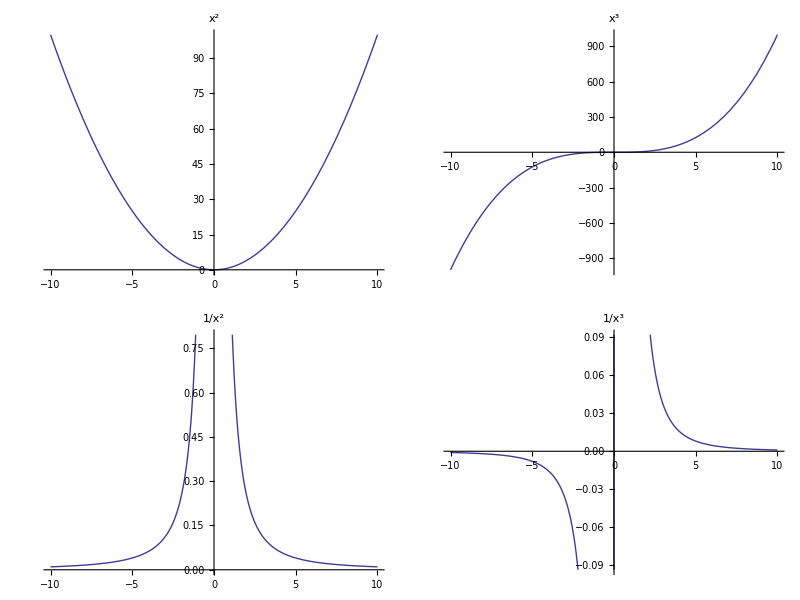

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[1]]],{f,{{x^2},{x^3}}}],Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[1]]],{f,{{x^-2},{x^-3}}}]
}]
```

#### 对数函数

对数函数：y=log_tx

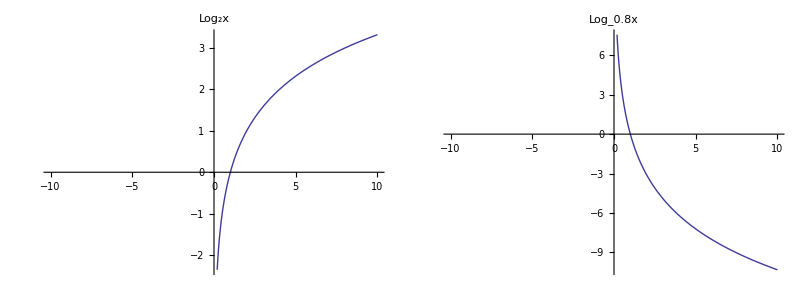

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[2]]],{f,{{Log[2,x],"Log_2x"},{Log[0.8,x],"Log_0.8x"}}}]
}]
```

#### 三角函数

三角函数：

Sin[x],Cos[x],Tan[x],Cot[x]

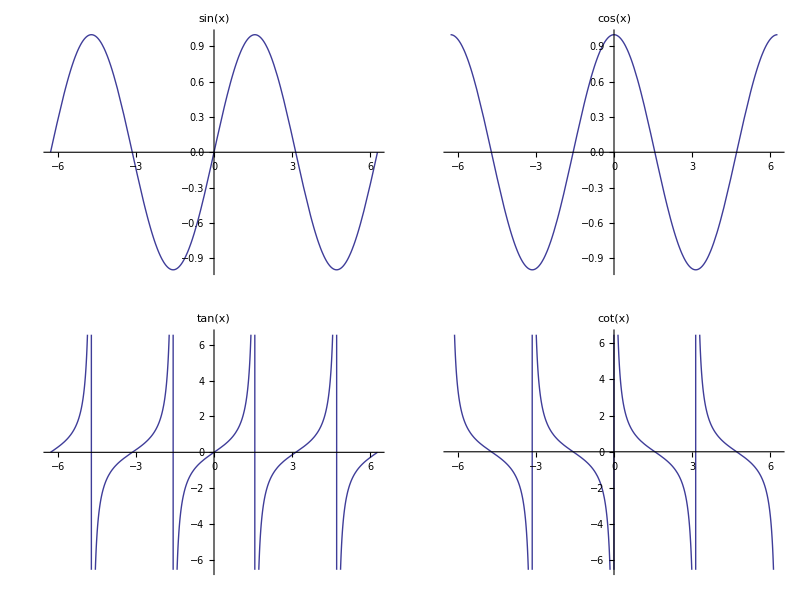

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-2Pi,2Pi},PlotLabel->f[[1]]],{f,{{Sin[x]},{Cos[x]}}}],
Table[Plot[f[[1]],{x,-2Pi,2Pi},PlotLabel->f[[1]]],{f,{{Tan[x]},{Cot[x]}}}]
}]
```

#### 反三角函数

反三角函数：

ArcSin[x],ArcCos[x],ArcTan[x],ArcCot[x]

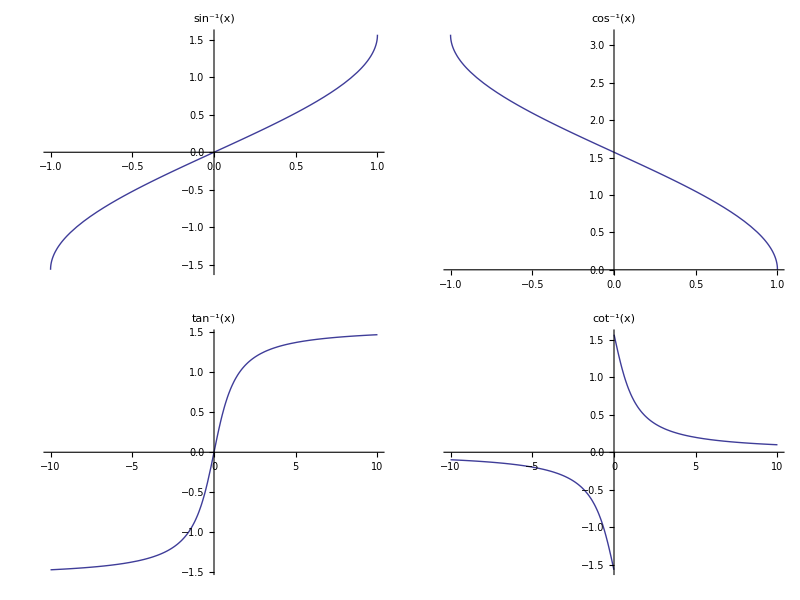

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-1,1},PlotLabel->f[[1]]],{f,{{ArcSin[x]},{ArcCos[x]}}}],
Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[1]]],{f,{{ArcTan[x]},{ArcCot[x]}}}]
}]
```

#### 双曲函数

双曲函数：

Sinh[x],Cosh[x],Tanh[x],Coth[x]

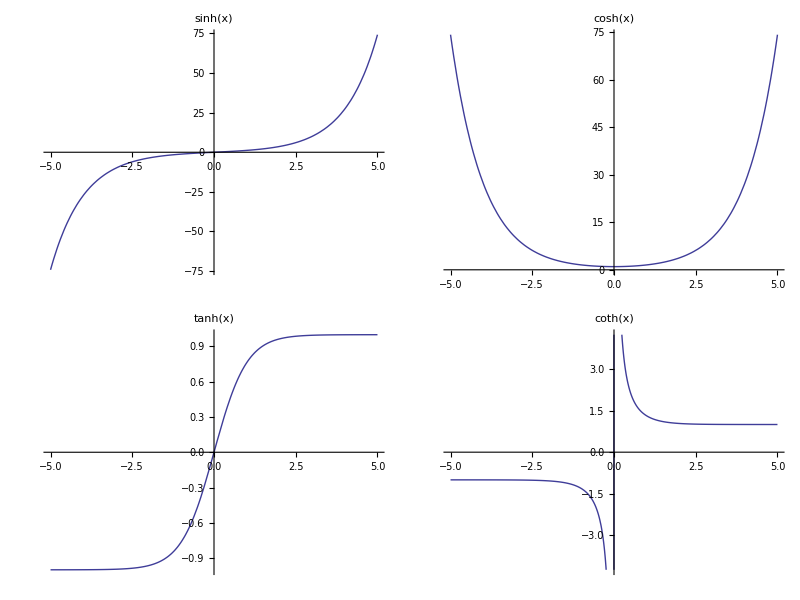

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-5,5},PlotLabel->f[[1]]],{f,{{Sinh[x]},{Cosh[x]}}}],
Table[Plot[f[[1]],{x,-5,5},PlotLabel->f[[1]]],{f,{{Tanh[x]},{Coth[x]}}}]
}]
```

#### 反双曲函数

反双曲函数：

ArcSinh[x],ArcCosh[x],ArcTanh[x],ArcCoth[x]

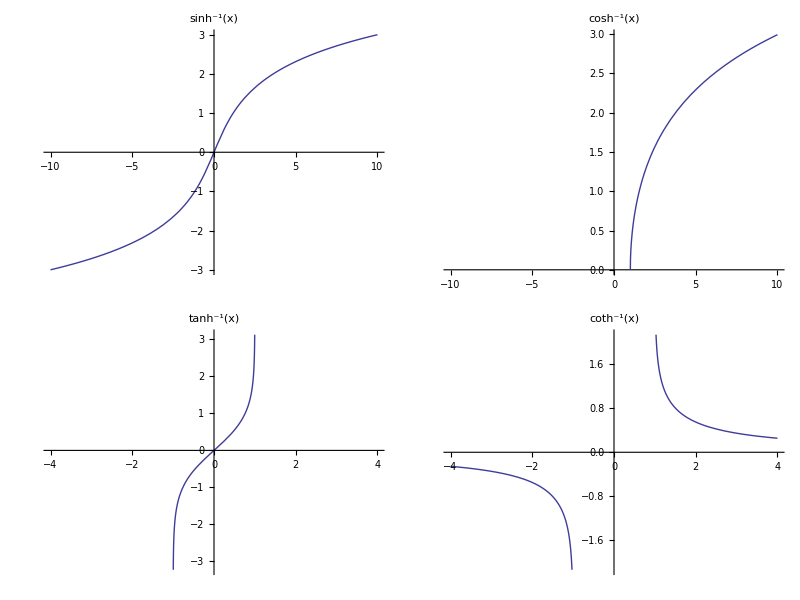

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[1]]],{f,{{ArcSinh[x]},{ArcCosh[x]}}}],
Table[Plot[f[[1]],{x,-4,4},PlotLabel->f[[1]]],{f,{{ArcTanh[x]},{ArcCoth[x]}}}]
}]
```

#### 其他常见函数

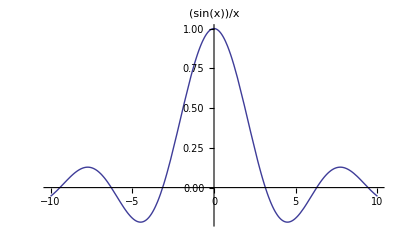
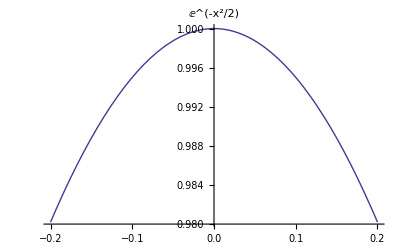
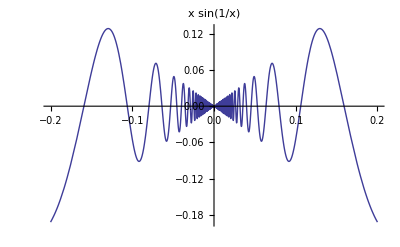
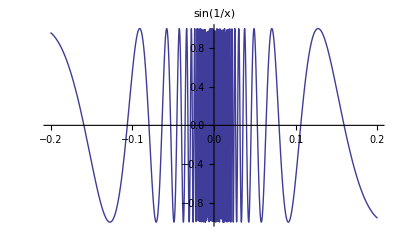
-Graphics- | 
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-10,10},PlotLabel->f[[1]]],{f,{{Sin[x]/x}}}],
Table[Plot[f[[1]],{x,-0.2,0.2},PlotLabel->f[[1]]],{f,{{Exp[-x^2/2]}}}],
Table[Plot[f[[1]],{x,-0.2,0.2},PlotLabel->f[[1]]],{f,{{x Sin[1/x]},{Sin[1/x]}}}]
}]
```

## Drafts

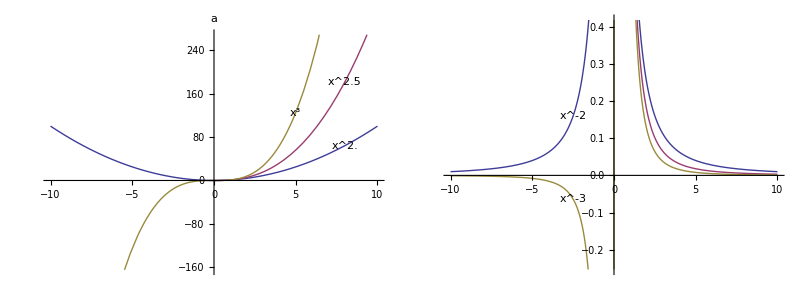

```mathematica
Grid[{{Plot[{x^2.,x^2.5,x^3.},{x,-10,10},Epilog->Append[Table[Inset[DisplayForm[x^t],{8,8^t}],{t,2,2.5,0.5}],Inset[DisplayForm[x^3],{5,5^3}]],PlotLabel->"a",ImageSize->imgSize],
Plot[{x^-2,x^-2.5,x^-3},{x,-10,10},Epilog->{Inset["x^-2",{-2.5,(-2.5)^-2}],Inset["x^-3",{-2.5,(-2.5)^-3}]},ImageSize->imgSize]}}]
```

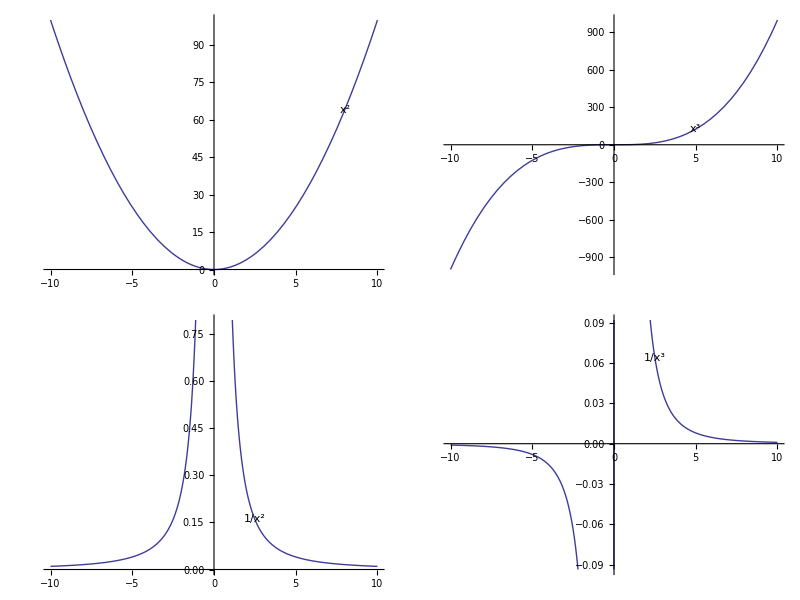

```mathematica
Grid[{
Table[Plot[f[[1]],{x,-10,10},Epilog->Inset[DisplayForm[f[[1]]],f[[2]]]],{f,{{x^2,{8,8^2}},{x^3,{5,5^3}}}}],Table[Plot[f[[1]],{x,-10,10},Epilog->Inset[DisplayForm[f[[1]]],f[[2]]]],{f,{{x^-2,{2.5,2.5^-2}},{x^-3,{2.5,2.5^-3}}}}]
}]
```